```mathematica
ClearAll["Global`*"]
```

```mathematica
table0061 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,06_1.txt",{"Table", "Data"}];
table0061[[All,1]]=table0061[[All,1]]-table0061[[1,1]];
table0061[[All,2]]=((table0061[[All,2]]+0.002)/(0.0043×1.67197));
table0061[[All,2]]=table0061[[All,2]]-Min[table0061[[All,2]]];
```

```mathematica
table0062 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,06_2.txt",{"Table", "Data"}];
table0062[[All,1]]=table0062[[All,1]]-table0062[[1,1]];
table0062[[All,2]]=((table0062[[All,2]]+0.002)/(0.0043×1.67197));
table0062[[All,2]]=table0062[[All,2]]-Min[table0062[[All,2]]];
```

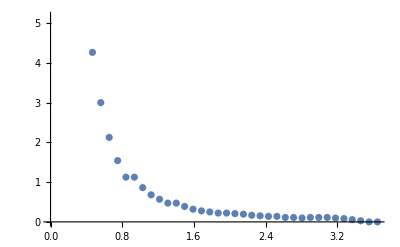

```mathematica
ListPlot[table0062]
```

```mathematica
table0063 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,06_3.txt",{"Table", "Data"}];
table0063[[All,1]]=table0063[[All,1]]-table0063[[1,1]];
table0063[[All,2]]=((table0063[[All,2]]+0.002)/(0.0043×1.67197));
table0063[[All,2]]=table0063[[All,2]]-Min[table0063[[All,2]]];
```

```mathematica
table0064 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,06_4.txt",{"Table", "Data"}];
table0064[[All,1]]=table0064[[All,1]]-table0064[[1,1]];
table0064[[All,2]]=((table0064[[All,2]]+0.002)/(0.0043×1.67197));
table0064[[All,2]]=table0064[[All,2]]-Min[table0064[[All,2]]];
```

```mathematica
table0065 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,06_5.txt",{"Table", "Data"}];
table0065[[All,1]]=table0065[[All,1]]-table0065[[1,1]];
table0065[[All,2]]=((table0065[[All,2]]+0.002)/(0.0043×1.67197));
table0065[[All,2]]=table0065[[All,2]]-Min[table0065[[All,2]]];
```

```mathematica
Export["table0061.dat",table0061];Export["table0062.dat",table0062];Export["table0063.dat",table0063];Export["table0064.dat",table0064];Export["table0065.dat",table0065];
```

```mathematica
T[k_,T0_,Tout_,t_]:=Tout+(T0-Tout)×Exp[-k×t]
```

```mathematica
fit0061=FindFit[table0061,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→9.68959,T0→86.2088,Tout→0.803894}

```mathematica
fit0062=FindFit[table0062,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→9.85512,T0→46.7696,Tout→0.695393}

```mathematica
fit0063=FindFit[table0063,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→12.0544,T0→77.0721,Tout→0.68012}

```mathematica
fit0064=FindFit[table0064,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→13.1017,T0→50.9526,Tout→0.56802}

```mathematica
fit0065=FindFit[table0065,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→7.93503,T0→62.4117,Tout→1.27487}

```mathematica
k0061=Mean[{k/.fit0061,k/.fit0062,k/.fit0063,k/.fit0064,k/.fit0065}]
```

10.5272

```mathematica
StandardDeviation[{k/.fit0061,k/.fit0062,k/.fit0063,k/.fit0064,k/.fit0065}]
```

2.05141

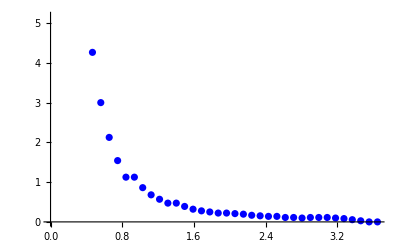

```mathematica
ListPlot[table0062,PlotStyle->Blue]
```

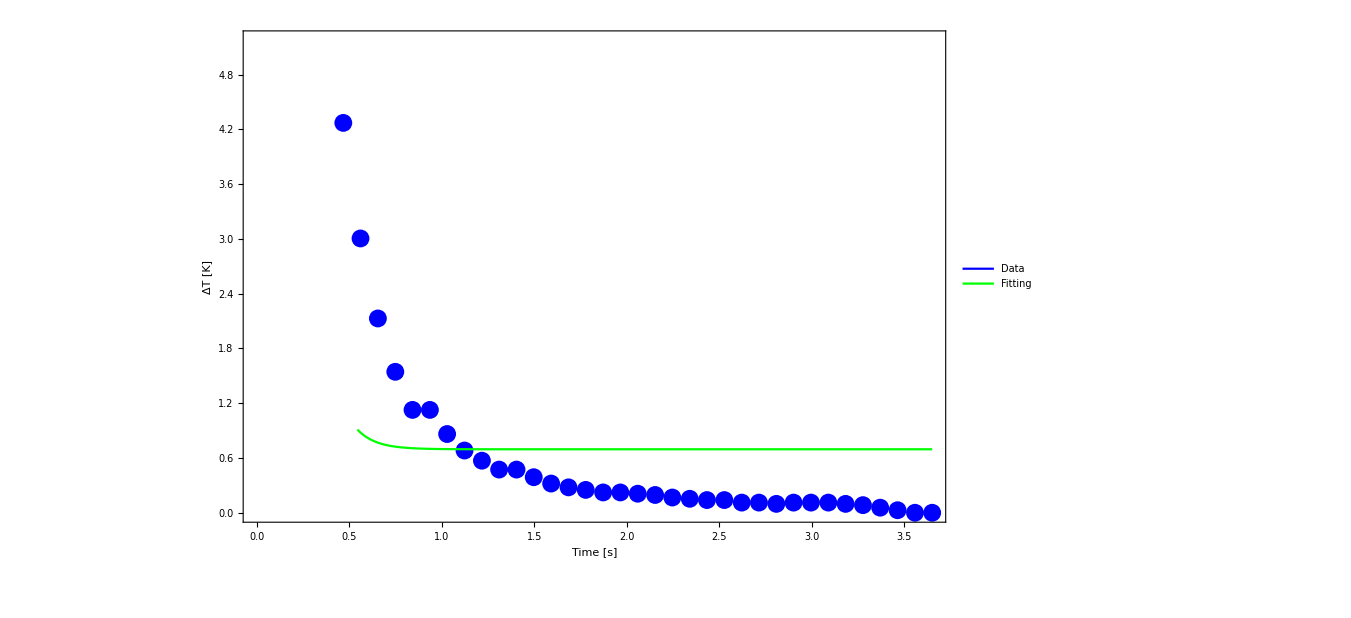

```mathematica
Legended[Show[ListPlot[table0062,PlotStyle->Blue],
Plot[T[k,T0,Tout,t]/.fit0062,{t,0,Max[table0062[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Time [s]","ΔT [K]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```